```mathematica
(*input: normalized auto-correlation, number of molecules, volume*)
Inp=
{{"G:\\Users\\rschulz\\Documents\\lignin_entropie\\vac300_1.cvs",1911/3,(4.52449*10^1-6.90580)},{"G:\\Users\\rschulz\\Documents\\lignin_entropie\\water\\vac300_0.cvs",2964/3,30.1768}}
```

{{G:\Users\rschulz\Documents\lignin_entropie\vac300_1.cvs,637,38.3391},{G:\Users\rschulz\Documents\lignin_entropie\water\vac300_0.cvs,988,30.1768}}

```mathematica
dir="G:\\Users\\rschulz\\Documents\\lignin_entropie\\water\\"
```

G:\Users\rschulz\Documents\lignin_entropie\water\

```mathematica
nInput = 2 ;(*change this to compute results for a differrent input*)
```

```mathematica
k=8.31451070*10^-3;
m=18.0153
h=0.3990313224
```

18.0153

0.399031

```mathematica
T=300;
nMol = Inp[[nInput,2]]
```

988

```mathematica
vol=SparseArray[{300->30.2169,360->32.1952,420->35.3154,480->40.8668}]
```

SparseArray[<4>,{480}]

```mathematica
ArrayRules[nMol/vol]
```

Power::infy: Infinite expression 1/0 encountered.

{{300}→32.6969,{360}→30.6878,{420}→27.9765,{480}→24.1761,{_}→ComplexInfinity}

```mathematica
file = Inp[[nInput,1]]
```

G:\Users\rschulz\Documents\lignin_entropie\water\vac300_0.cvs

```mathematica
S[T_,nMol_, file_,vol_]:=Module[{c1, Ct,gT,j,h1,rho,De,f1,f,gg,Dw,gs,Sig,fy,z,SHs,Wgs,hb,beta,Who,Svib,Sconf,Srot},c1=k*T*3 *nMol; Ct=Import[file,"Table"] ; Ct[[All,2]]=Ct[[All,2]]*c1;gT=2/k /T*.004*(Chop[Fourier[Ct[[All,2]],FourierParameters->{1,1}]+Fourier[Ct[[All,2]],FourierParameters->{1,-1}] - Ct[[1,2]]]);j[f_,y_]:=2*y^3*f^3-(y+6y^2)*f^2+(2+6y)*f-2;h1[f_,D_]:=j[f,(f/D)^(3/2)];rho=nMol/vol;De=2*gT[[1]]/9/nMol*(Pi*k*T/m)^(1/2)*rho^(1/3)*(6/Pi)^(2/3);f1=f/.ToRules[Reduce[h1[f,De]==0,f,Reals]];gg[w_]:=gT[[1]]/(1+(gT[[1]]*w/(12*f1*nMol))^2);Dw=2*Pi/10;gs[w_]:=gT[[1+w/Dw]]-gg[w];Sig= k*(Log[1/rho*(4*Pi*m*3/2*nMol*k*T/(3*nMol*h^2))^(3/2)]+5/2);z[y_]:=(1+y+y^2-y^3)/(1-y)^3;fy=f1*(f1/De)^(3/2);SHs=Sig+k*(Log[z[fy]]+fy*(3*fy-4)/(1-fy)^2);Wgs=1/3*SHs/k;hb=h/2/Pi;beta=1/k/T;Who[w_]:=beta*hb*w/(Exp[beta*hb*w]-1)-Log[1-Exp[-beta*hb*w]];Svib=k*Sum[Dw/2/Pi*gs[w]*Who[w],{w,Dw,1/.008*2*Pi,Dw}];Sconf=k*Sum[Dw/2/Pi*gg[w]*Wgs,{w,0,1/.008*2*Pi,Dw}];Srot=.04448*nMol;
(Svib+Sconf)]
```

```mathematica
For[T=300,T≤480,T+=60, l=Map[Function[i,fn=ToString[T]<>"_"<>ToString[i];S[T,nMol,dir<>"vac"<>fn<>".cvs",Import[dir<>"vol"<>fn<>".dat","Table"][[1,2]]]],Range[0,80,20]];Print[ToString[T]<>" " <>ToString[Mean[l]]<>" " <>ToString[StandardDeviation[l]]]];
```

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed ⟦ 1, 2 ⟧ is longer than depth of object.

Import::nffil: File not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Set::partd: Part specification Ct$17450 ⟦ All, 2 ⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Fourier::fftl: Argument Symbol[] is not a non-empty list or rectangular array of numeric quantities.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol :: argx will be suppressed during this calculation.

Fourier::fftl: Argument Symbol[] is not a non-empty list or rectangular array of numeric quantities.

Part::partd: Part specification $Failed ⟦ 1, 2 ⟧ is longer than depth of object.

$Aborted

30.1768

```mathematica
Plot[-39255.6-T*-39255.6,T]
```

Plot::pllim: Range specification T is not of the form {x, xmin, xmax}.

Plot[-39255.6-T (-39255.6),T]

```mathematica
Plot[-39255.6-T (-39255.6),T,300,480]
```

Plot::nonopt: Options expected (instead of 480) beyond position 2 in Plot[-39255.6` - T (-39255.6`), T, 300, 480]. An option must be a rule or a list of rules.

Plot[-39255.6-T (-39255.6),T,300,480]

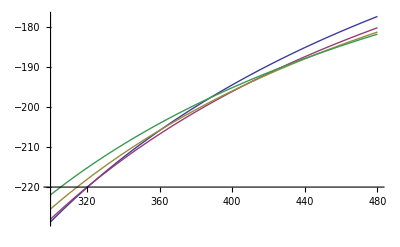

```mathematica
Plot[{(-39255.6+3/4*nMol*k*(T-300)-T 97.8589)/T,(-36087.5+3/4*nMol*k*(T-360)-T*106.515)/T,(-32818.5+3/4*nMol*k*(T-420)-T*113.627)/T,(-29189.6+3/4*nMol*k*(T-480)-T*120.95)/T},{T,300,480}]
```